```mathematica
Print["Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! \n Run: Get[\"https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m\"] for installation"];
Needs["IGraphM`"];
```

Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/armin/my_programs/alphaLoopMisc/graph_generation/example

```mathematica
allGraphs=ToExpression["{"<>StringDrop[StringReplace[Import["ggHH.qgr","Text"],{"**NewDiagram**"->",","\n"->""}]<>"}",1]];
```

```mathematica
allGraphs[[1,2]]
```

{{in1→5,in[gluon[p1]]},{in2→5,in[gluon[p2]]},{1→out1,out[higgs[p3]]},{2→out2,out[higgs[p4]]},{1→3,t[-k1]},{4→1,t[-k1-p3]},{3→2,t[k2]},{2→4,t[k2+p4]},{3→5,gluon[-k1-k2]},{4→5,gluon[k1+k2+p3+p4]}}

```mathematica
(* represent graph by: {{edge1,tag1:List},...,{edgeN,tagN:List}} *)
ClearAll[findIsomorphicGraphs]
findIsomorphicGraphs[graphs_:List]:=Block[{tagging,taggingToNum,$uniqueTag, graphsEdgeColored,graphsEdgeColoredSimple,isIsomorph,twr,$myAssoc,isomorphisms},
SetAttributes[twr,Orderless];
(* taggings become colors on edge-colored graphs, multiple taggings will be translated to single prime which becomes the color of the edge *)
tagging=Variables@(graphs[[All,All,2]]);
If[Length@tagging≠0,
tagging=tagging,
tagging=$uniqueTag
];
(* start prime range late, so that translation of multi-edge graphs is still unique *)
taggingToNum=Thread@(Rule[tagging,Prime[Range[100,Length@tagging+99]]]);
(*graphIsomorph=Table[IGIsomorphicQ[Graph@graph[i],Graph@graph[j]],{i,1,Length[momenta]},{j,1,Length[momenta]}]//LowerTriangularize;
isomorphisms=(Position[graphIsomorph,True]/. {i_,i_}-> Nothing);
*)
(* translate to undirected graphs and apply tagging *)
graphsEdgeColored=graphs /. taggingToNum /. {Rule[a_,b_],x_List}:>{twr[a,b],Times@@x} /. {TwoWayRule[a_,b_],x_List}:>{twr[a,b],Times@@x};
(* translate to undirected edge colored graphs {a<->b,tagPrime}->{a<->b,tagPrime}*)
graphsEdgeColored =Sort/@graphsEdgeColored;
(* get isomorphism for graphs which are isomorphic; IGVF2 needed for multi-edge graphs: 
	There is no algorithm working for multi-edge graphs directly. Therefore translate into edge-colored simple graphs! The color is the multiplicity of the edge e.g.: g1Multiedge={{1<->4,5},1<->4,5}} --> g1ColouredSimple={1<->4->2*5}*)
graphsEdgeColoredSimple=(Counts/@graphsEdgeColored) /.Association:>$myAssoc/.Rule[List[twr[a_,b_],color1_],color2_]:> Rule[twr[a,b],color1*color2] /. twr->TwoWayRule /. $myAssoc:>Association;
(* thats a bit of laziness, since over computation of half the entries.... *)
isIsomorph=Table[IGVF2IsomorphicQ[{Graph[VertexList[Keys@graph1],Keys[graph1]],"EdgeColors"->graph1},{Graph[VertexList[Keys@graph2],Keys[graph2]],"EdgeColors"->graph2}],{graph1,graphsEdgeColoredSimple},{graph2,graphsEdgeColoredSimple}]//LowerTriangularize;
isomorphisms=(Position[isIsomorph,True]/. {i_,i_}-> Nothing)
]
```

```mathematica
findIsomorphicGraphs[allGraphs[[All,2]]/. gluon[x__]:>mg /. t[x__]:>mt /. ghost[x__]:>mgo /. {Rule[a_,c_],b_}:>{Rule[a,c],{b}}]
```

{{3,2},{5,4},{7,6},{8,6},{8,7},{9,6},{9,7},{9,8},{12,11},{14,13},{16,15},{19,17},{20,18},{25,21},{26,22},{27,23},{28,24},{30,29},{32,31},{34,33},{36,35},{38,37},{39,35},{39,36},{40,35},{40,36},{40,39},{41,37},{41,38},{42,37},{42,38},{42,41},{44,43},{45,43},{45,44},{46,43},{46,44},{46,45},{48,47},{50,49},{51,47},{51,48},{52,47},{52,48},{52,51},{53,49},{53,50},{54,49},{54,50},{54,53},{56,55},{58,57},{59,55},{59,56},{60,55},{60,56},{60,59},{61,57},{61,58},{62,57},{62,58},{62,61},{64,63},{66,65},{68,67},{70,69},{71,69},{71,70},{72,69},{72,70},{72,71},{74,73},{75,73},{75,74},{76,73},{76,74},{76,75},{78,77},{79,77},{79,78},{80,77},{80,78},{80,79},{81,77},{81,78},{81,79},{81,80},{82,77},{82,78},{82,79},{82,80},{82,81},{83,77},{83,78},{83,79},{83,80},{83,81},{83,82},{84,77},{84,78},{84,79},{84,80},{84,81},{84,82},{84,83},{86,85},{88,87},{91,89},{92,90},{93,85},{93,86},{94,85},{94,86},{94,93},{95,87},{95,88},{96,87},{96,88},{96,95},{97,89},{97,91},{98,90},{98,92},{99,89},{99,91},{99,97},{100,90},{100,92},{100,98},{102,101},{105,103},{106,104},{107,103},{107,105},{108,104},{108,106},{109,103},{109,105},{109,107},{110,104},{110,106},{110,108},{112,111},{115,113},{116,114},{117,113},{117,115},{118,114},{118,116},{119,113},{119,115},{119,117},{120,114},{120,116},{120,118},{122,121},{123,121},{123,122},{124,121},{124,122},{124,123},{126,125},{128,127},{130,129},{132,131},{133,125},{133,126},{134,125},{134,126},{134,133},{135,127},{135,128},{136,127},{136,128},{136,135},{137,129},{137,130},{138,129},{138,130},{138,137},{139,131},{139,132},{140,131},{140,132},{140,139},{142,141},{143,141},{143,142},{144,141},{144,142},{144,143}}

```mathematica
ClearAll[plotGraph]
plotGraph[graph_,imSize_:Scaled[0.5]]:=Module[{},
Print[GraphComputation`GraphPlotLegacy[graph,Method->{"SpringElectricalEmbedding", "RepulsiveForcePower" -> -1.55},EdgeRenderingFunction->({{RGBColor[0.22,0.34,0.63],Arrowheads[0.015],Arrow[#]},If[#3=!=None,Text[#3,Mean[#1],Background->White],{}]}&),MultiedgeStyle->.3,SelfLoopStyle->All,ImageSize->imSize]]
]
```

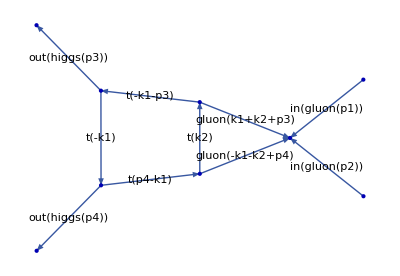

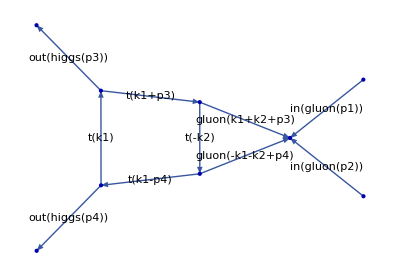

{Null,Null}

```mathematica
plotGraph[#,Scaled[.5]]&/@allGraphs[[2;;3,2]]
```